```mathematica
lt[{x_,v_,tau_},h_] := {Mod[x + v h,2 Pi, -Pi], v - h Sin[x + v h] - k Cos[tau+h],tau + h}
```

```mathematica
phi1[{x_,v_,tau_},h_] := {Mod[x + v h,2 Pi, -Pi], v, tau + h}
```

```mathematica
phi2[{x_,v_,tau_},h_] := {x, v - h Sin[x + v h] - k Cos[tau+h],tau}
```

```mathematica
strang[{x_,v_,tau_}, h_,tmax_] := Module[{n = IntegerPart[tmax/h]},
first = phi2[{x,v,tau},-h/2];
last = Nest[lt[#, h] &, first,n];
last = phi2[last,h/2];
Delete[last,3]
]
```

```mathematica
MyListPlot[list_] := ListPlot[list,ImageSize->900,AspectRatio->1]
```

```mathematica
k=0.001;
```

```mathematica
Poincare[{x_,v_}, h_] := strang[{x,v,0}, h, 2 Pi]
```

```mathematica
PoincareN[{x_, v_}, h_, n_] := NestList[Poincare[#,h] &, {x,v}, n]
```

```mathematica
PoincarePlot[h_, n_] := Module[{},
(*part1 = Table[
PoincareN[{0,v},h,n], {v,0.5,1.5,0.2}
];*)
(*part1 = Table[
PoincareN[{0,v},h,n], {v,1.9,2.1,0.1}
];*)
part1 = PoincareN[{0,1.95},h,n];
(*part2 = Table[
PoincareN[{0,v},h,n], {v,1.5,2,0.1}
];*)
(*part3= Table[
PoincareN[{0,v},h,n], {v,2,5,1}
];*)
(*Join[part1, part2,part3] // MyListPlot*)
part1// MyListPlot
]
```

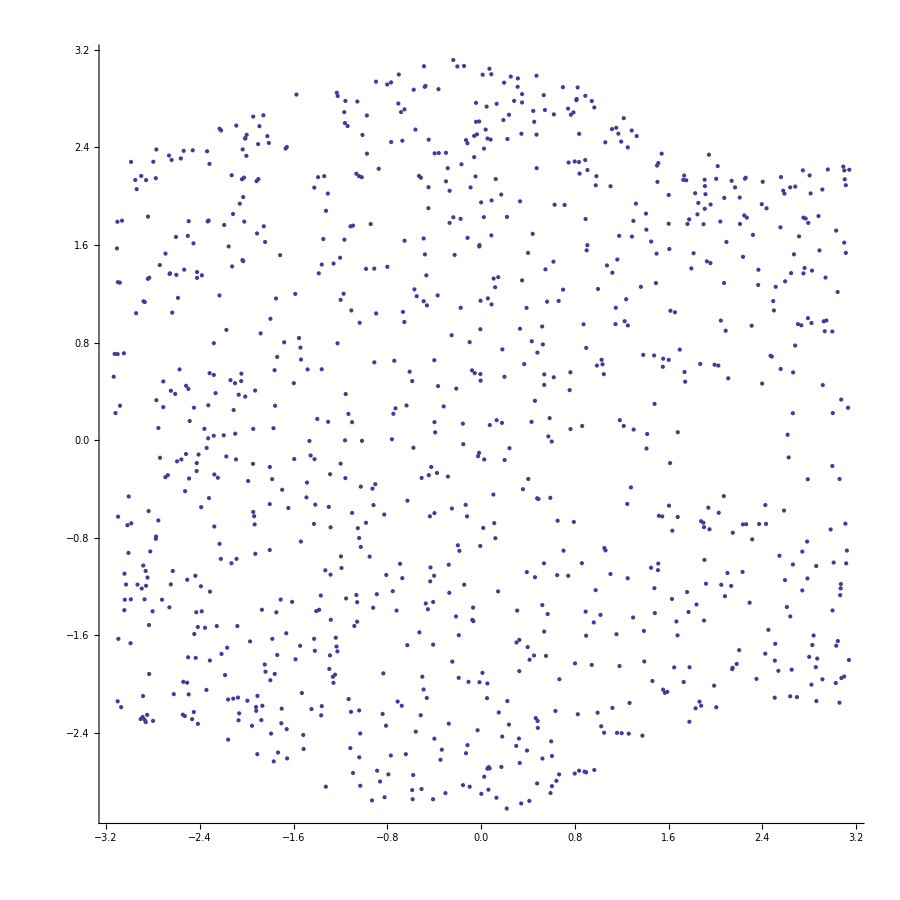

```mathematica
PoincarePlot[0.001,1000]
```